# Vacuum Stability

```mathematica
ClearAll["Global`*"];
```

```mathematica
g=0.65;
gY=0.36;
yt=0.9945;
Q=150;
mh=125.;
v=174.;
```

```mathematica
V0[λ_,A_,μH_,μS_,h_,S_]:=1/4 λ h^4-1/2 μH^2 h^2+1/2 μS^2 S^2-1/2 A S h^2;
mW[h_]:=1/4 g^2 h^2;
mZ[h_]:=1/4(g^2+gY^2)h^2;
mt[h_]:=1/2 yt^2 h^2;
VCW[λ_,A_,μH_,μS_,h_]:=1/(64 π^2)(6 mW[h]^2(Log[mW[h]/Q^2]-5/6)+3 mZ[h]^2(Log[mZ[h]/Q^2]-5/6)-12 mt[h]^2(Log[mt[h]/Q^2]-3/2));
V0T[λ_,A_,μH_,μS_,h_,S_]:=V0[λ,A,μH,μS,h,S]+VCW[λ,A,μH,μS,h]-(V0[λ,A,μH,μS,10^-10,10^-10]+VCW[λ,A,μH,μS,10^-10]);
```

```mathematica
μH2[mS_,sinθ_]:=(mh^2 mS^2)/(2(sinθ^2 mh^2+(1-sinθ^2)mS^2));
μS2[mS_,sinθ_]:=sinθ^2 mh^2+(1-sinθ^2)mS^2;
A2[mS_,sinθ_]:=((mh^2-mS^2)^2 sinθ^2(1-sinθ^2))/(2 v^2);
λ[mS_,sinθ_]:=((1-sinθ^2)mh^2+sinθ^2 mS^2)/(4 v^2);
√μH2[5,0.17]
√μS2[5,0.17]
√A2[5,0.17]
λ[5,0.17]
```

20.2598

21.8138

10.6204

0.125299

```mathematica
Plot3D[{V0T[0.125299,10.6204,20.2598,21.8138,h,S]},{h,0,500},{S,0,3000}]
```

-Graphics3D-

```mathematica
FindMinimum[V0T[0.125299,10.6204,20.2598,21.8138,h,S],{h,S}]
```

{-626264.,{h→85.0835,S→80.7865}}

## Export

```mathematica
BP1‵V0T[h_,S_]=V0T[0.125299,10.6204,20.2598,21.8138,h,S];
DumpSave[NotebookDirectory[]<>"output/V0T_BP1.m",BP1‵V0T]
```

{BP1‵V0T}

## Check the bounce solution from simplebounce code

### Unit 100 GeV

```mathematica
pathdata=Drop[Import[NotebookDirectory[]<>"output/benchmark.csv","Data"][[2;;]],2];
Spath[h_]:=Interpolation[pathdata[[All,{2,3}]]][h];
hevolve[r_]:=Interpolation[pathdata[[All,{1,2}]]][r];
Sevolve[r_]:=Interpolation[pathdata[[All,{1,3}]]][r];
hpath[S_]:=Interpolation[pathdata[[All,{3,2}]]][S];
```

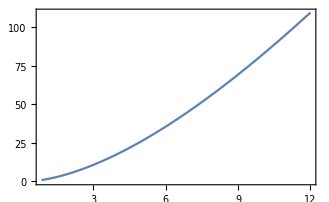

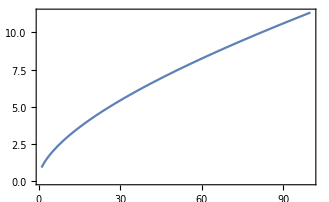

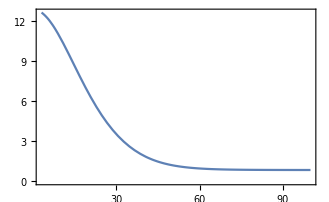

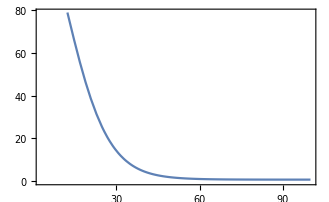

```mathematica
Plot[Spath[h],{h,.86,12.00}]
Plot[hpath[S],{S,1.00,100.00}]
Plot[hevolve[r],{r,3,100}]
Plot[Sevolve[r],{r,3,100}]
```

```mathematica
dV0Tdh[h_,S_]:=D[V0T[0.125299,10.6204,20.2598,21.8138,ϕ,S],{ϕ}]/.{ϕ->h};
dV0TdS[h_,S_]:=D[V0[0.125299,10.6204,20.2598,21.8138,h,ϕ],{ϕ}]/.{ϕ->S};
```

```mathematica
eqh[r_]:=hevolve''[r]+3/r hevolve'[r]-dV0Tdh[hevolve[r],Spath[hevolve[r]]];
eqs[r_]:=Sevolve''[r]+3/r Sevolve'[r]-dV0TdS[hpath[Sevolve[r]],Sevolve[r]];
```

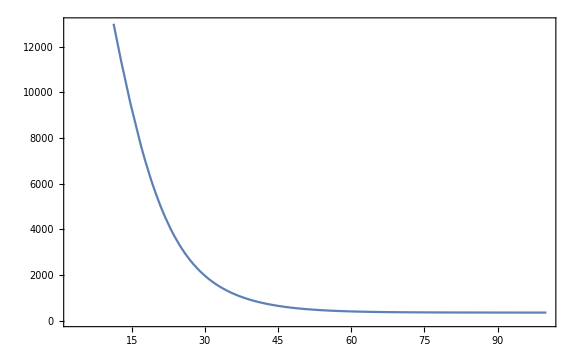

```mathematica
Plot[eqh[r],{r,3,100}]
```

```mathematica
eqh[80]
```

361.398

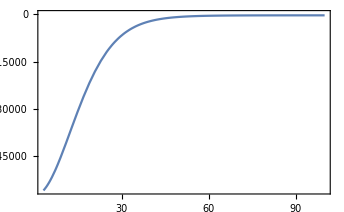

```mathematica
Plot[eqs[r],{r,3,100}]
```

### Unit GeV

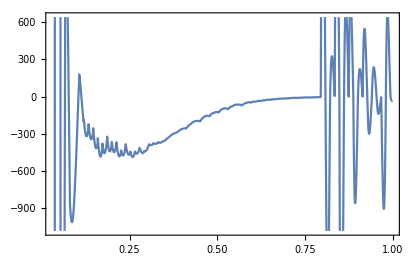

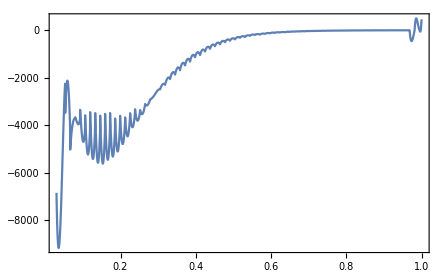

```mathematica
pathdata={0.01*#1,100*#2,100*#3}& @@@Drop[Import[NotebookDirectory[]<>"output/benchmark.csv","Data"][[2;;]],2];
Spath[h_]:=Interpolation[pathdata[[All,{2,3}]]][h];
hevolve[r_]:=Interpolation[pathdata[[All,{1,2}]]][r];
Sevolve[r_]:=Interpolation[pathdata[[All,{1,3}]]][r];
hpath[S_]:=Interpolation[pathdata[[All,{3,2}]]][S];
dV0Tdh[h_,S_]:=D[V0T[0.125299,10.6204,20.2598,21.8138,ϕ,S],{ϕ}]/.{ϕ->h};
dV0TdS[h_,S_]:=D[V0[0.125299,10.6204,20.2598,21.8138,h,ϕ],{ϕ}]/.{ϕ->S};
eqh[r_]:=hevolve''[r]+3/r hevolve'[r]-dV0Tdh[hevolve[r],Spath[hevolve[r]]];
eqs[r_]:=Sevolve''[r]+3/r Sevolve'[r]-dV0TdS[hpath[Sevolve[r]],Sevolve[r]];
Plot[eqh[r],{r,.03,1}]
Plot[eqs[r],{r,.03,1}]
```